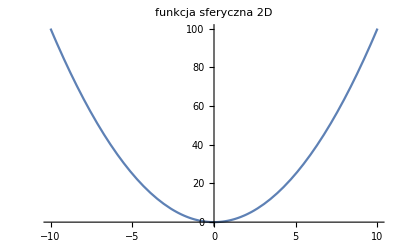

-Graphics3D-

```mathematica
(*Dawid Bitner*)
(*Zadanie 1-prezentacja wynków*)
(*zad1*)
(*funkcja sferyczna*)
SphereFunction2D[x_]=x^2; (*funkcja 2D*)
SphereFunction3D[x_,y_]=x^2+y^2; (*funkcja 2D*)
Plot[SphereFunction2D[x],{x,-10,10}, PlotLabel->"funkcja sferyczna 2D"] (*Wykres dla funkcji 2D*)
Plot3D[SphereFunction3D[x,y],{x,-10,10},{y,-10,10}, PlotLabel->"funkcja sferyczna 3D"] (*Wykres dla funkcji 2D*)
(*w poniższych przykładach w zad1 zostało wykonane to dokładnie tak jak dla tego, z tym, że dla innych funkcji*)
```

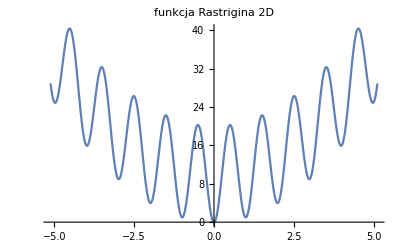

-Graphics3D-

```mathematica
(*funkcja Rastrigina*)
RastringerFunction2D[x_]=10+(x^2-10*Cos[2*Pi*x]);
RastringerFunction3D[x_,y_]=10+((x^2-10*Cos[2*Pi*x])+(y^2-10*Cos[2*Pi*y]));
Plot[RastringerFunction2D[x],{x,-5.12,5.12},PlotLabel->"funkcja Rastrigina 2D"]
Plot3D[RastringerFunction3D[x,y],{x,-5.12,5.12},{y,-5.12,5.12}, PlotLabel->"funkcja Rastrigina 3D"]
```

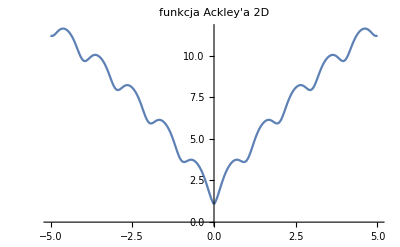

-Graphics3D-

```mathematica
(*funkcja Ackley'a*)
AckleyFunction2D[x_]=-20 Exp[-0.2*Sqrt[0.5*x^2]]-Exp[0.5*Cos[2*Pi*x]]+E+20;
AckleyFunction3D[x_,y_]=-20 Exp[-0.2*Sqrt[0.5*(x^2+y^2)]]-Exp[0.5*(Cos[2*Pi*x]+Cos[2*Pi*y])]+E+20;
Plot[AckleyFunction2D[x],{x,-5,5},PlotLabel->"funkcja Ackley'a 2D"]
Plot3D[AckleyFunction3D[x,y],{x,-5,5},{y,-5,5},PlotLabel->"funkcja Ackley'a 3D"]
```

```mathematica
(* dolina Rosenbrocka *)
```

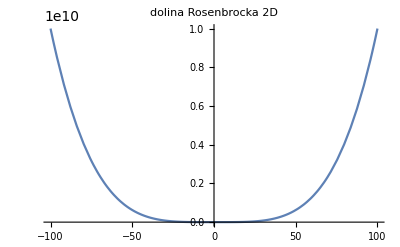

-Graphics3D-

```mathematica
RosenbrockFunction2D[x_]=100*(-x^2)^2+(1-x)^2;
RosenbrockFunction3D[x_,y_]=100*(y-x^2)^2+(1-x)^2;
Plot[RosenbrockFunction2D[x],{x,-100,100}, PlotLabel-> "dolina Rosenbrocka 2D"]
Plot3D[RosenbrockFunction3D[x,y],{x,-10,10},{y,-100,100}, PlotLabel-> "dolina Rosenbrocka 3D"]
```

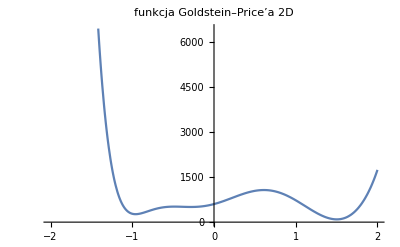

-Graphics3D-

```mathematica
(* funkcja Goldstein–Price’a *)
GoldsteinPriceFunction2D[x_]=(1+(x+1)^2*(19-14x+3x^2))*(30+(2x)^2*(18-32x+12x^2));
GoldsteinPriceFunction3D[x_,y_]=(1+(x+y+1)^2*(19-14x+3x^2-14y+6x*y+3y^2))*(30+(2x-3y)^2*(18-32x+12x^2+48y-36x*y+27y^2));
Plot[GoldsteinPriceFunction2D[x],{x,-2,2}, PlotLabel-> "funkcja Goldstein–Price’a 2D"]
Plot3D[GoldsteinPriceFunction3D[x,y],{x,-2,2},{y,-2,2}, PlotLabel-> "funkcja Goldstein–Price’a 3D"]
```

```mathematica
(* funkcja Hölder table *)
HolderTableFunction3D[x_,y_]=-Abs[Sin[x]*Cos[y]*Exp[Abs[1- (Sqrt[x^2+y^2])/Pi]]];
Plot3D[HolderTableFunction3D[x,y],{x,-10,10},{y,-10,10}, PlotLabel->"funkcja Hölder table 3D"]
```

-Graphics3D-

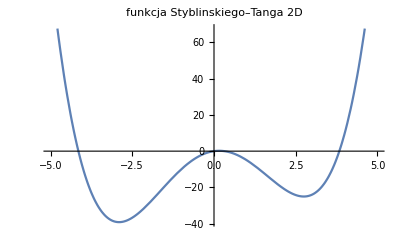

-Graphics3D-

```mathematica
(* funkcja Styblinskiego–Tanga *)
StyblinskiTangFunction2D[x_]=(x^4-16x^2+5x)/2;
StyblinskiTangFunction3D[x_,y_]=((x^4+y^4)-16*(x^2+y^2)+5*(x+y))/2;
Plot[StyblinskiTangFunction2D[x], {x,-5,5},PlotLabel->"funkcja Styblinskiego–Tanga 2D"]
Plot3D[StyblinskiTangFunction3D[x,y],{x,-5,5},{y,-5,5}, PlotLabel-> "funkcja Styblinskiego–Tanga 3D"]
```

```mathematica
(*zad2*)
PML[it_,numberOfPoints_,f_,down_,upper_]:=Module[{x,y,points,bests={},values={},bestScores={},averages={}},
(*program szukający minimum funkcji testowej*)
(*
m - liczba iteracji;
numberOfPoints - liczba iteracji;
f- funkcja testowa;
down - wartość dolna x i y;
top - wartość górna x i y;
values - wartości punktów funkcji
*)
For[i=1,i≤it,i++, (*pętla przebiega tyle razy ile zadał to użytkownik w parametrze it*)
points={};
values={};
For[j=1,j≤numberOfPoints,j++, (*pętla przebiega tyle razy ile chce użytkownik, liczba punktów zadana przez użytkownika *)
x=RandomReal[{down[[1]],upper[[1]]}];(*losujemy punkty pseudolosowe*)
y=RandomReal[{down[[2]],upper[[2]]}];
points=Append[points,{x,y}];
values=Append[values,f[x,y]];]; (* oblicza wartość funkcji w punktach wylosowanych *)
minimum=Min[values]; (* wyznacza najmniejszą wartość funkcji *)
pos=Position[values,minimum]; (* pobiera wartość najmniejszej pozycji w tablicy *)
best=points[[pos[[1]]]]; (* gdyby zdarzył się 2 takie same wartości, wybieramy pierwszą - wcześniejszą i oznaczamy jako najlepszą *)
avg=Mean[values]; (* wyznacza średnią wartość funkcji *)
(* zmienne lokalne ale w obrębie całej funkcji *)
bests=Append[bests,{minimum,best[[1,1]],best[[1,2]]}];
bestScores=Append[bestScores,minimum];
averages=Append[averages,avg];];
bestPos=Position[bests,Min[bestScores]];
Print["Najlepszy: ",bests[[bestPos[[1,1]],1]]," w punkcie: ",bests[[bestPos[[1,1]],2]],",",bests[[bestPos[[1,1]],3]]]; (*poniżej wypisywanie wyników*)
Print[ListPlot[bestScores, PlotLabel->"Najlepsze"] ]; (*Wykres przebiegu wartości optymalnej w kolejnych iteracjach powinien być dyskretny. Zgodnie z tym komentarzem zamieniłem 
ListLinePlot na ListPlot *) 
Print[ListPlot[averages, PlotLabel->"Średnie"]];
Print[bestScores];
Print[averages];

];
```

Najlepszy: -19.1762 w punkcie: 8.10916,9.6817

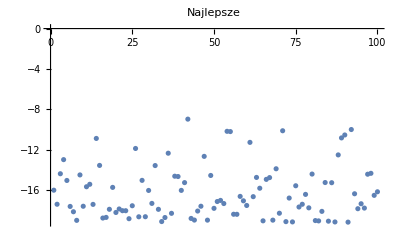

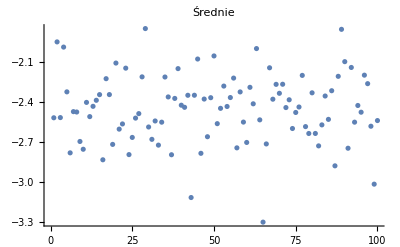

{-16.0125,-17.4047,-14.3824,-12.9843,-15.0474,-17.6203,-18.1474,-18.9994,-14.4991,-17.6027,-15.67,-15.4277,-17.418,-10.8844,-13.5576,-18.7709,-18.7073,-17.9037,-15.7335,-18.2192,-17.873,-18.0425,-18.0453,-18.8362,-17.5533,-11.8781,-18.6471,-15.0377,-18.6402,-16.0362,-17.3204,-13.571,-17.9067,-19.1198,-18.7197,-12.3478,-18.3033,-14.6258,-14.6577,-16.0304,-15.2604,-8.97165,-18.8097,-18.9719,-18.0771,-17.6013,-12.6608,-18.978,-14.5523,-17.8087,-17.135,-17.0238,-17.3341,-10.1786,-10.2052,-18.3951,-18.401,-16.6259,-17.0637,-17.5259,-11.2735,-16.6525,-14.7472,-15.8165,-19.0471,-14.9402,-14.7648,-18.979,-13.8891,-18.2939,-10.1234,-19.1276,-16.7908,-19.1533,-15.5727,-17.6774,-17.4062,-16.4276,-17.7603,-14.4139,-19.0212,-19.0545,-18.1099,-15.2523,-19.0807,-15.2702,-19.1574,-12.5162,-10.8317,-10.542,-19.1762,-10.002,-16.3657,-17.8459,-17.3552,-17.7839,-14.4291,-14.3405,-16.5218,-16.1691}

{-2.51956,-1.94948,-2.5181,-1.98847,-2.32482,-2.78305,-2.47337,-2.47627,-2.69753,-2.75597,-2.40399,-2.51084,-2.43344,-2.38813,-2.34562,-2.83513,-2.22582,-2.34529,-2.71949,-2.10845,-2.60475,-2.56582,-2.14664,-2.79621,-2.66716,-2.52196,-2.48828,-2.21212,-1.84935,-2.58876,-2.68152,-2.5435,-2.72499,-2.55253,-2.21324,-2.3629,-2.79726,-2.37408,-2.15023,-2.42505,-2.44086,-2.35051,-3.11869,-2.35018,-2.0781,-2.78653,-2.37884,-2.66179,-2.36865,-2.05494,-2.56368,-2.44855,-2.2814,-2.43468,-2.36749,-2.22136,-2.74547,-2.32526,-2.55187,-2.70488,-2.29072,-2.41461,-1.99962,-2.53522,-3.3035,-2.71604,-2.14397,-2.3799,-2.26837,-2.33567,-2.26763,-2.4428,-2.38433,-2.60011,-2.4796,-2.43852,-2.20107,-2.58583,-2.63759,-2.33204,-2.63731,-2.73068,-2.57296,-2.35597,-2.53147,-2.3163,-2.88054,-2.20812,-1.85502,-2.0979,-2.74829,-2.14154,-2.55246,-2.42714,-2.47762,-2.19933,-2.26321,-2.58302,-3.01815,-2.54046}

```mathematica
(*zad3*)
PML[100,100,HolderTableFunction3D, {-10,-10}, {10,10}];
(*przedstawia działanie metody PML na przykładzie funkcji Holder Table*)
```

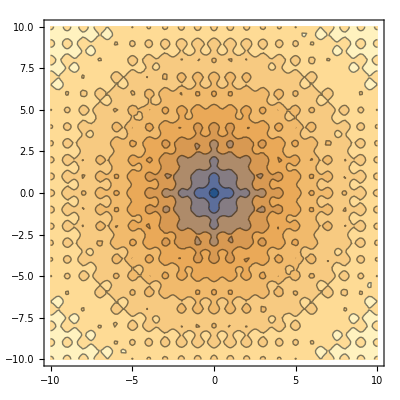

```mathematica
(*zad4*)
(*Procedura pokazująca ruch punktu x_opt na płąszczyźnie na tle wykresu warstwicowego funkcji*)
ContourPlot[AckleyFunction3D[x,y],{x,-10,10},{y,-10,10}]
```